# Script to Generate Regular Patterns for ERACR

## Functions

```mathematica
SetDirectory[NotebookDirectory[]];
<<PajaroLocoPublic`
PolarToCartesian[r_,θ_]:={r*Cos[θ],r*Sin[θ]}
CartesianToPolar[x_,y_]:={Sqrt[x^2+y^2],ArcTan[y/x]}
FormatForMGDrivE[latLongs_,popSize_]:={#[[1]],#[[2,1]],#[[2,2]],popSize}&/@Transpose[{Range[latLongs//Length],latLongs//N}]
```

## Routine

-Graphics-

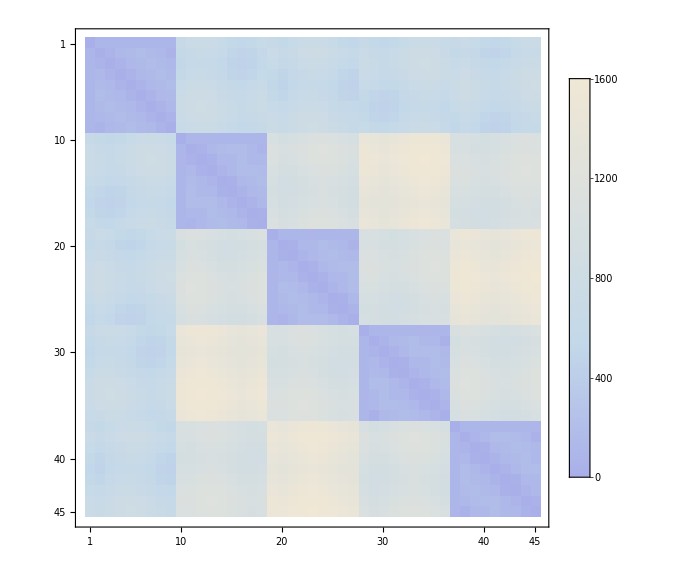

```mathematica
angles=Range[0,2π-π/4,π/4];
step=50;
radii=Range[step,50,step];
anglesRing=Range[0,2π-π/2,π/2];
{radiusRing,phaseRing}={750,π/4};
noiseLevel=0;
(**)
templatePoints=Table[PolarToCartesian[i,#]&/@angles,{i,radii}];
pointPattern=Prepend[Flatten[templatePoints,1],{0,0}];
(**)
ringCentroids=PolarToCartesian[radiusRing,#]&/@(anglesRing+phaseRing);
fullSet=Flatten[{pointPattern,Table[(i+#)&/@pointPattern,{i,ringCentroids}]//Flatten[#,1]&},1];
fullSetNoisy={#[[1]]+RandomReal[{-noiseLevel,noiseLevel}],#[[2]]+RandomReal[{-noiseLevel,noiseLevel}]}&/@fullSet//N;
clustered=FindClusters[fullSetNoisy,Method->"NeighborhoodContraction"];
(**)
callouts=ListPlot[Table[Callout[fullSet[[i]],i,Background->None,LabelStyle->{6}],{i,1,Length[fullSet]}],PlotStyle->Opacity[0]];
listPlot=ListPlot[clustered,
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
Axes->None,
PlotStyle->PointSize[Large],
ImageSize->Large
];
callouts=Show[listPlot,callouts,ImageSize->Large]
(**)
distances=Table[N[EuclideanDistance[i,#]]&/@fullSetNoisy,{i,fullSetNoisy}];
matrixPlot=MatrixPlot[distances,ColorFunction->"LakeColors",PlotLegends->Automatic,ImageSize->Large]
```

## Analyze Kernel

```mathematica
kernel=Import["FiveCities_Kernel.csv"];
coordinates=Import["FiveCities_Coordinates.csv"][[All,2;;3]];
graph=WeightedAdjacencyGraph[kernel,VertexCoordinates->coordinates];
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45
0.315037 | 0.40924 | 0.40924 | 0.40924 | 0.40924 | 0.40924 | 0.40924 | 0.40924 | 0.40924 | 0.31504 | 0.409247 | 0.409248 | 0.409247 | 0.409247 | 0.409245 | 0.409244 | 0.409245 | 0.409247 | 0.31504 | 0.409245 | 0.409247 | 0.409247 | 0.409248 | 0.409247 | 0.409247 | 0.409245 | 0.409244 | 0.31504 | 0.409245 | 0.409244 | 0.409245 | 0.409247 | 0.409247 | 0.409248 | 0.409247 | 0.409247 | 0.31504 | 0.409247 | 0.409247 | 0.409245 | 0.409244 | 0.409245 | 0.409247 | 0.409247 | 0.409248)

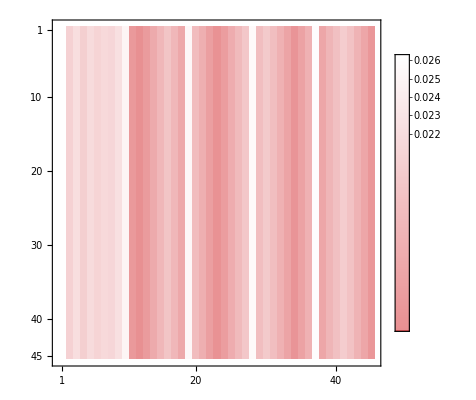

```mathematica
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,5->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
{Range[Length[kernel]],MarkovProcessProperties[markov,"HoldingTimeMean"]}//MatrixForm
MarkovProcessProperties[markov,"LimitTransitionMatrix"]//MatrixPlot[#,PlotLegends->Automatic,ColorFunction->"CherryTones"]&
```

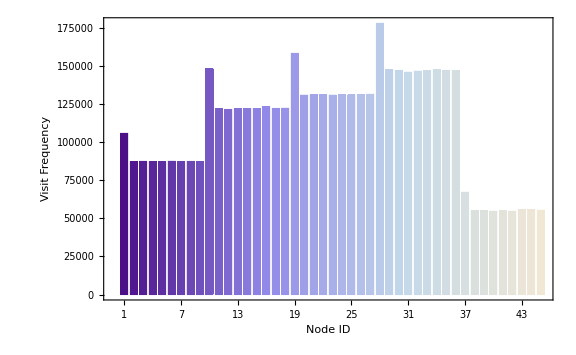

randomWalkerFrequencyMarkov.pdf

```mathematica
data=RandomFunction[markov,{0,5000000}];
tally=(data//Normal)[[All,All,2]][[1]]//Tally//Sort;
BarChart[tally[[All,2]],
ChartStyle->"LakeColors",
ChartLabels->tally[[All,1]],
ImageSize->Large,
Frame->True,
FrameStyle->Thick,
FrameTicksStyle->Directive[8],
FrameLabel->(Style[#,25]&/@{"Node ID","Visit Frequency"})
]
Export["randomWalkerFrequencyMarkov.pdf",%,ImageSize->1500,ImageResolution->500]
```

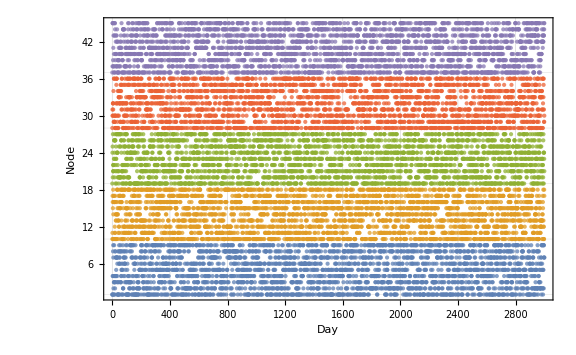

```mathematica
initialState=Table[ConstantArray[0,kernel//Length]//ReplacePart[#,i->1]&,{i,{1,10,19,28,37}}];
markov=DiscreteMarkovProcess[#,kernel]&/@initialStates;
data=RandomFunction[#,{0,3000}]&/@markov;
ListPlot[data,
Filling->None,
PlotRange->{All,{1,kernel//Length}},
Frame->True,
FrameStyle->Thick,
ImageSize->Large,
GridLines->{Range[0,100000,100],Range[1,50,9]},
GridLinesStyle->Directive[Gray,Opacity[.2]],
FrameLabel->(Style[#,20]&/@{"Day","Node"}),
(*AspectRatio->1,*)
PlotStyle->Directive[Opacity[.75],PointSize[Medium]],
ImageSize->Large
]
(*Export["randomWalkerMarkov.pdf",%,ImageSize->1500,ImageResolution->500]*)
```

## Export

```mathematica
formattedList=FormatForMGDrivE[fullSet,50];
Export["FiveCities_Coordinates.csv",formattedList]
Export["FiveCities_Distances.csv",distances]
Export["FiveCities.png",Grid[{{listPlot,matrixPlot,callouts}}],ImageResolution->250]
```

FiveCities_Coordinates.csv

FiveCities_Distances.csv

FiveCities.png